# Homework 7 Erik Worth

## 1.

a)

```mathematica
j0[x_] := Sin[x]/x
```

```mathematica
y0[x_] := Cos[x]/x
```

```mathematica
jn[x_,n_] := Module[{u = j0[x]},
Do[u =Simplify[(1/x)*D[u, x]], {n}];Simplify[((-1)^n)(x^n) u]]
```

```mathematica
yn[x_,n_] := Module[{u = y0[x]},
Do[u =Simplify[(1/x)*D[u, x]], {n}];Simplify[((-1)^n)(-x^n) u]]
```

b)

```mathematica
jn[x,0]
```

Sin[x]/x

```mathematica
j1[x_] = jn[x,1]
```

(-x Cos[x]+Sin[x])/x^2

```mathematica
jn[x,10]
```

-1/x^11(55 x (11904165-1670760 x^2+51597 x^4-468 x^6+x^8) Cos[x]+(-654729075+310134825 x^2-18918900 x^4+315315 x^6-1485 x^8+x^10) Sin[x])

```mathematica
yn[x,0]
```

-Cos[x]/x

```mathematica
y1[x_] = yn[x,1]
```

-(Cos[x]+x Sin[x])/x^2

```mathematica
yn[x,10]
```

1/x^11((-654729075+310134825 x^2-18918900 x^4+315315 x^6-1485 x^8+x^10) Cos[x]-55 x (11904165-1670760 x^2+51597 x^4-468 x^6+x^8) Sin[x])

c)

```mathematica
Series[jn[x,10], {x,0,14}]
```

x^10/13749310575-x^12/632468286450+x^14/63246828645000+O[x]^15

```mathematica
Series[yn[x,10], {x,0,-7}]
```

-654729075/x^11-34459425/(2 x^9)-2027025/(8 x^7)+1/O[x]^6

d)

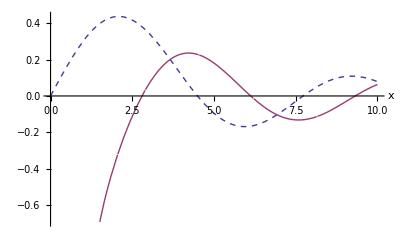

```mathematica
Plot[{j1[x], y1[x]},{x,0,10}, PlotStyle-> {Dashing[{0.01, 0.01}], Dashing[{1,0}]}, AxesLabel -> Automatic]
```

The spherical Bessel functions with n = 0 j0 and y0 are are defined as functions of x. The general spherical Bessel functions (jn and yn) are defined as functions of n and x which iteratively apply Raleigh's formula to an internal variable u, which is initially defined to be j0 or y0, respectively. In part b) the 0th, 1st and 10th spherical bessel functions are produced by jn and yn.  In part d) jn[x,1] and yn[x, 1] are plotted on the same graph. j1 is the dashed line; y1 is the solid line.

## 2.

a)

```mathematica
ser = Series[Tanh[x], {x,0,20}]
```

x-x^3/3+(2 x^5)/15-(17 x^7)/315+(62 x^9)/2835-(1382 x^11)/155925+(21844 x^13)/6081075-(929569 x^15)/638512875+(6404582 x^17)/10854718875-(443861162 x^19)/1856156927625+O[x]^21

b)

```mathematica
InverseSeries[ser]
```

x+x^3/3+x^5/5+x^7/7+x^9/9+x^11/11+x^13/13+x^15/15+x^17/17+x^19/19+O[x]^21

The series ser is created as the series representation of tanh(x) about x = 0 up to order 20. InverseSeries then acts on ser to produce the series for tan(x) about 0.

## 3.

a)

```mathematica
Assuming[{T < θ, T >0, θ > 0},{9((T/θ)^3)Integrate[(x^4)Exp[x]/(Exp[x]-1)^2, {x, 0, Infinity}]}]
```

{(12 π^4 T^3)/(5 θ^3)}

b)

```mathematica
9((T/θ)^3)Integrate[(x^4)/(x)^2, {x, 0, θ/T}]
```

```mathematica
3
```

c)

```mathematica
Clear[x]
```

```mathematica
f[x_] =Assuming[{x>0},9((1/x)^3)Integrate[(x^4)Exp[x]/(Exp[x] -1)^2, {x,0,x}]] // Simplify
```

(9 (-(4 π^4)/15+4 ⅈ π x^3+(ⅇ^x x^4)/(1-ⅇ^x)+4 x^3 Log[-1+ⅇ^x]+12 x (x PolyLog[2,ⅇ^x]-2 PolyLog[3,ⅇ^x])+24 PolyLog[4,ⅇ^x]))/x^3

```mathematica
y = 1/x;
```

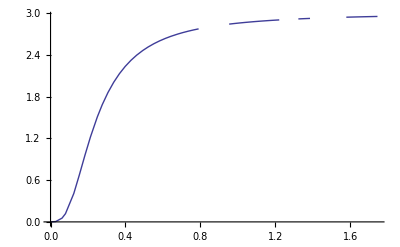

```mathematica
Plot[f[y], {x, 0, 100}, PlotRange->Automatic]
```

In part a), since T << θ , the upper limit of integration is taken to be infinity. Integrate[] is used to analytically integrate the function, which is helped along by assuming that T < θ, and both T and θ are positive. In part b), since T >> θ, x tends to be very small, so Exp[x] tends towards 1 and Exp[x] - 1 can be approximated as x. Integrate[] is then used to do the simplified integral. In part c), the integral is performed without any approximations and plotted against T/θ. The function appears to approach 3 assymptotically as T/θ gets larger, which is consistent with the result from part b).

## 4.

a)

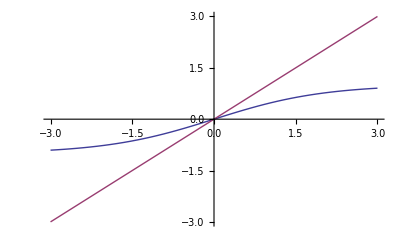

```mathematica
Plot[{Tanh[0.5u], u}, {u, -3, 3}]
```

b)

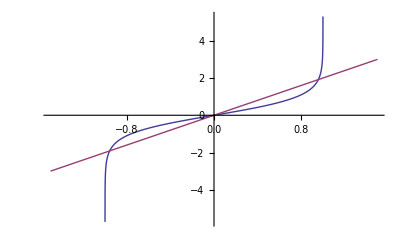

```mathematica
Plot[{ArcTanh[u], 2u}, {u, -1.5, 1.5}]
```

c) see attached paper

d-e)

```mathematica
g1 =Plot[m /. Solve[m^2 - 3(1 - T)== 0, m],{T, 0.05, 1.1}];
```

```mathematica
g2= Plot[3(1-T), {T, 0.05, 1.1}];
```

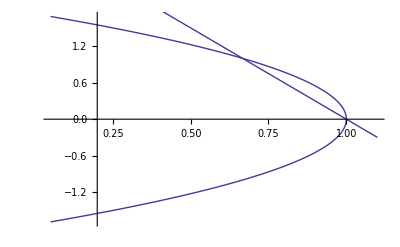

```mathematica
Show[g1, g2]
```

In part a), T < J, and so m is multiplied by some factor between 0 and 1. I chose T/J to be 0.5 arbitrarily and plotted Tanh[0.5m] and clearly the only solution is at m = 0. For T > J the argument of Tanh[] must be greater than 1. I arbitrarily chose the ratio to be 2 and plotted Tanh[2m] and there are two non-zero solutions in the vicinity of ±1. In parts d) and e) m and the high temperature approximation for m^2 are plotted against T/T_c on the same graph.

## 5.

```mathematica
Clear["Global`*"]
```

```mathematica
g = 9.81;
```

```mathematica
k = 0.004;
```

```mathematica
xmax[vv_] := (k = 0.004;v = vv; tfinal[theta_] :=(sol=  NDSolve [ { x''[t] == -k x'[t]Sqrt[y'[t]^2 + x'[t]^2] , y''[t] == -k y'[t]Sqrt[y'[t]^2 + x'[t]^2] -g,x[0] == 0, y[0] == 0, x'[0] == v Cos[theta],y'[0] == v Sin[theta] }, {x, y}, {t, 0, 100}] ; yy[t_] = y[t] /. sol[[1]]; xx[t_] = x[t] /. sol[[1]];  t/.  FindRoot[ yy[t] , {t, 1, 40}, MaxIterations -> 500]);  xfinal[theta_?NumericQ] := xx[tfinal[theta]]; FindMaximum[xfinal[theta], {theta, 0.1, 1.3}][[1]])
```

```mathematica
xmax2[vv_] := (k = 0; v = vv; tfinal[theta_] :=(sol=  NDSolve [ { x''[t] == -k x'[t]Sqrt[y'[t]^2 + x'[t]^2] , y''[t] == -k y'[t]Sqrt[y'[t]^2 + x'[t]^2] -g,x[0] == 0, y[0] == 0, x'[0] == v Cos[theta],y'[0] == v Sin[theta] }, {x, y}, {t, 0, 100}] ; yy[t_] = y[t] /. sol[[1]]; xx[t_] = x[t] /. sol[[1]];  t/.  FindRoot[ yy[t] , {t, 1, 40}, MaxIterations -> 500]);  xfinal[theta_?NumericQ] := xx[tfinal[theta]]; FindMaximum[xfinal[theta], {theta, 0.1, 1.3}][[1]])
```

a)

```mathematica
xmax[50]
```

150.21

```mathematica
xmax2[50]
```

254.842

b)

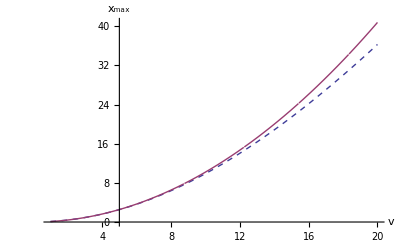

```mathematica
Plot[{xmax[v], xmax2[v]}, {v, 1, 20},AxesLabel->{"v","x_max"},PlotStyle-> {Dashing[{0.01, 0.01}], Dashing[{1,0}]}]
```

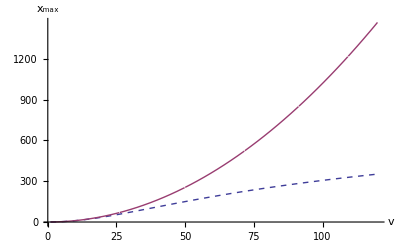

```mathematica
Plot[{xmax[v], xmax2[v]}, {v, 1, 120},AxesLabel->{"v","x_max"},PlotStyle-> {Dashing[{0.01, 0.01}], Dashing[{1,0}]}]
```

Functions xmax and xmax2 are defined as functions of initial velocity vv. Xmax has a friction coeffient k = 0.004, while xmax2 does not have friction. Both functions define the function tfinal, which is a function of the launch angle θ. It solves the equations of motion and produces the total time the ball spends in the air. Xfinal finds the x coordinate at tfinal. FindMaximum varies θ from 0.1 to 1.3 and selects the largest value of xfinal, producing the longest range possible.

We can see that the difference between the simulations with friction and without friction produce very different ranges; the frictionless launch goes over 100 meters farther.

In part b) the functions xmax and xmax2 are plotted against initial velocity on the same graph. The frictionless case is the solid line, the case with friction is dashed. One graph is a low initial velocity case, where v is varied between 1 and 20 and we see that friction makes little difference; the maximum ranges only start to differ significantly as v gets larger than 15 m/s. In the second graph, v is varied betwen 1 and 120 and a huge difference in maximum range is evident. The frictionless case is increasing without bound, while the case with friction is plateuing. At v = 120 m/s the difference between the two maximum ranges is around 1000 meters.

## 6.

a)

```mathematica
Clear["Global`*"]
f[x_] := 4 λ x (1 - x);
```

```mathematica
λ=0.2;g1 =  ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 0.2" ];
```

```mathematica
λ=0.6;g2 =  ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 0.6" ];
```

```mathematica
λ=0.8;g3 =  ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 0.8" ];
```

```mathematica
λ=0.84;g4 =  ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 0.84" ];
```

```mathematica
λ=0.90;g5 =  ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 0.90" ];
```

```mathematica
λ=0.961;g6 =  ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 0.961" ];
```

```mathematica
λ=0.97;g7 =  ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 0.97" ];
```

```mathematica
λ=1;
g8 =  ListPlot [ {NestList[f, 0.5, 10],NestList[f, 0.5, 10]} ,Joined -> {True, False}, Axes -> False, Frame -> True, FrameLabel -> {"n","x_n"}, PlotMarkers -> Automatic, RotateLabel -> False,PlotLabel -> "λ = 1" ];
```

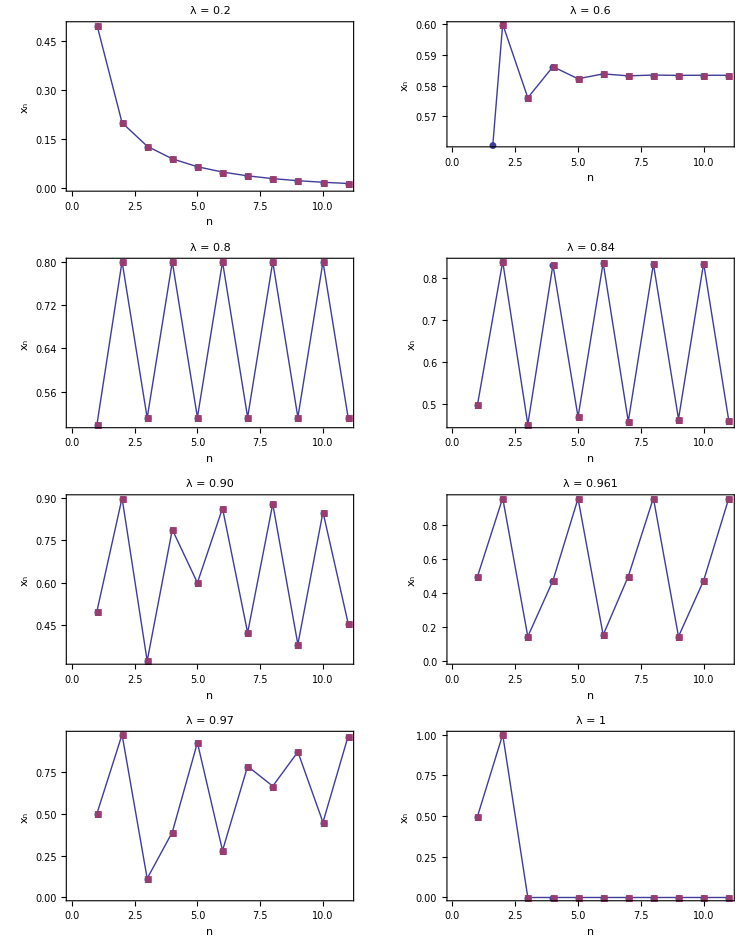

```mathematica
Show[GraphicsGrid[{{g1,g2},{g3,g4}, {g5, g6}, {g7, g8}},Spacings->Scaled[0.05]]]
```

```mathematica
lya [l_, xinit_, n_, ndrop_] := (λ = l;xlist =Drop[  NestList[f,xinit,  n] ,  ndrop+1 ]; 
Apply[ Plus, Log[ Abs[ f'[xlist] ] ] ] / Length[xlist])
```

```mathematica
l1 =lya[0.2, 0.7, 50000, 20]
```

-0.223144

```mathematica
l2 =lya[0.6, 0.7, 50000, 20]
```

-0.916291

```mathematica
l3 =lya[0.8, 0.7, 50000, 20]
```

-0.91629

```mathematica
l4 =lya[0.84, 0.7, 50000, 20]
```

-0.281411

```mathematica
l5 = lya[0.90, 0.7, 50000, 20]
```

0.181605

```mathematica
l6 = lya[0.961, 0.7, 50000, 20]
```

-0.280341

```mathematica
l7 = lya[0.97, 0.7, 50000, 20]
```

0.463027

```mathematica
l8 =lya[1, 0.7, 50000, 20]
```

0.693132

c)

```mathematica
iterate [ m_,  n_]  := Drop [ NestList [f, 0.5, n], m]
```

```mathematica
drawpt[y_] := Point[{λ, y}]
```

```mathematica
graph[λmin_,λmax_, nλ_, mdrop_, n_] := Graphics [ {PointSize[0.001],Table [ Map[drawpt, iterate [mdrop,n ] ], {λ, λmin, λmax, (λmax-λmin)/nλ} ]}]
```

```mathematica
Show[graph[0.934,0.94,400,300,700],Axes->False,Frame->True,FrameLabel->{"λ","x"},PlotRange->{{0.934,0.94},{0,1}},AspectRatio->1]
```

-Graphics-

d)

```mathematica
Show[graph[0.9352,0.9359,400,300,700],Axes->False,Frame->True,FrameLabel->{"λ","x"},PlotRange->{{0.9352,0.9359},{0.4743,0.5119}},AspectRatio->1]
```

-Graphics-

e)

```mathematica
Clear[ λ, x]
```

```mathematica
Show[graph[0.72,1,400,300,700],Axes->False,Frame->True,FrameLabel->{"λ","x"},PlotRange->{{0.72,1.02},{0,1}},AspectRatio->1]
```

```mathematica
f2[x_] = f[f[x]] ;
```

```mathematica
FindRoot[{f[x] == x, f'[x] == 1}, {x,0.2},  {λ,0.2}]
```

{x→5.97024×10^-9,λ→0.25}

```mathematica
λ[0] = 0.25
```

0.25

```mathematica
FindRoot[{f[x] == x, f'[x] == -1}, {x,0.5},  {λ,0.5}]
```

{x→0.666667,λ→0.75}

```mathematica
λ[1] = 0.75
```

0.75

```mathematica
FindRoot[{f2[x] == x, f2'[x] == -1}, {x,0.65},  {λ,0.75}]
```

{x→0.43996,λ→0.862372}

```mathematica
λ[2] = 0.8623724356957946
```

0.862372

```mathematica
f4[x_] := f2[f2[x]]
```

```mathematica
FindRoot[{f4[x] == x, f4'[x] == -1}, {x, 0.88}, {λ, 0.9}]
```

{x→0.88405,λ→0.886023}

```mathematica
λ[3] = 0.8860225898879807
```

0.886023

```mathematica
f8[x_] := f4[f4[x]]
```

```mathematica
FindRoot[{f8[x] == x, f8'[x] == -1}, {x,0.891}, {λ,0.891}]
```

{x→0.890787,λ→0.891102}

```mathematica
λ[4] = 0.8911018165238584
```

0.891102

```mathematica
f16[x_] := f8[f8[x]]
```

```mathematica
FindRoot[{x == f16[x] , f16'[x] == -1}, {x, 0.892}, {λ,0.892}]
```

{x→0.89214,λ→0.89219}

```mathematica
λ[5] = 0.8921898548851404
```

0.89219

```mathematica
Print [ k, "       ", Subscript[δ, k]]; 
Do[ Print[n , "      ", ( λ[n] - λ[n-1])/(λ[n+1] - λ[n])], {n, 1, 4}]
```

k       δ_k

1      4.44949

2      4.75145

3      4.65625

4      4.66824

In part a) we can see fixed point behavior for λ = 0.2 and 0.6; λ = 0.2 is tending towards 0 while λ = 0.6 hits a fixed point around 0.58. For λ = 0.8 and 0.84 we see limit cycle behavior; λ = 0.80 has period 2 and λ = 0.84 appears to have been period doubled to 4. λ = 0.90 is chaotic, and λ = 0.961 is exhibiting limit cycle behavior with period 2. λ = 0.97 is chaotic again, while λ = 1 drops to a fixed point of 0 very quickly. 

In part b), the Lyapunov exponents verify the graphs in part a) in most cases. The positive exponents correspond to the chaotic looking graphs, λ = 0.90 and λ = 0.97.  All the negative exponents correspond to graphs with non-chaotic behavior, fixed points and limit cycles. The other positive exponent corresponds to λ = 1, which appears in the graph to quickly converge to a fixed point of 0. I do not understand this discrepency.

Initially the graph in part c) was plotted from λ = 0.75 to λ = 1. The final graph was produced by changing the range of λ to zoom in on a non-chaotic region that had 5 horizontal lines, corresponding to a period 5 limit cycle.

Using the Get Coordinates function in the drop down menu for the graph in part c), new ranges for x and λ were plotted to zoom in on one branch in the period 5 limit cycle. Period doubling is evident again, with periods 10, 20, 40, and so on visible, then chaos appears.

In part e) f2[x] is defined as f[f[x], f4[x] = f2[f2[x]] and so on. FindRoot is used to find the values of x and λ where f[x] = x and f’[x] = -1.  The value of λ corresponds to the point where the previous limit cycle becomes unstable and the period doubles. The value for λ is stored in an array of λ values, and the process is repeated for f2[x] and so on. FindRoot is helped by providing guesses for its starting values for x and λ. These are obtained by using the Get Coordinates function on the full-scale graph produced at the beginning of part e). The first 4 δ_ks are computed and printed in a table; after 4 iterations the value for δ_kis very close to the Feigenbaum constant. The value of δ_kis 4.666824... and the Feigenbaum constant is 4.66920... so they are around 0.001 apart.

## 7.

```mathematica
f[x_] := λ Sin[Pi x]
```

a)

```mathematica
lya [l_, xinit_, n_, ndrop_] := (λ = l;xlist =Drop[  NestList[f,xinit,  n] ,  ndrop+1 ]; 
Apply[ Plus, Log[ Abs[ f'[xlist] ] ] ] / Length[xlist])
```

```mathematica
L = lya[0.9, 0.7, 50000, 20]
```

0.352352

b)

```mathematica
λ = N[9/10, 3000];
```

```mathematica
Subscript[x, 0]= N[4/10, 3000];
```

```mathematica
Subscript[x, 5000]=AccountingForm[Nest[f, Subscript[x, 0], 5000], 5]
```

0.79559

```mathematica
Precision[Subscript[x, 5000]]
```

2250.98

In part a) the same function lya[] from problem 6 is used to compute the Lyapunov exponent for λ = 0.9. It is positive, so it is clear that this is a chaotic region. In part b), λ and x_0 are defined to be 0.4 and 0.9 to 3000 digits of precision. The precision of these values was chosen because we are trying to find x_5000 and to maintain accuracy it appears you need precision of about 0.6 times the number of iterations. x_5000 is computed and displayed with 5 digits; its precision is computed to be 2250.